```mathematica
cA0=1;
```

```mathematica
k1=1;
```

```mathematica
cb[t_,k2_]=k1/(k2-k1)cA0(Exp[-k1*t]-Exp[-k2*t])
```

(ⅇ^-t-ⅇ^(-k2 t))/(-1+k2)

```mathematica
cb[t,.5*k1]
```

-2. (ⅇ^-t-ⅇ^(-0.5 t))

```mathematica
cb[100,.5*k1]
```

3.8575×10^-22

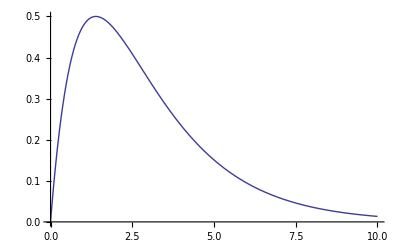

```mathematica
Plot[cb[t,.5k1],{t,0,10}]
```

```mathematica
cb[t,.05k1]
```

-1.05263 (ⅇ^-t-ⅇ^(-0.05 t))

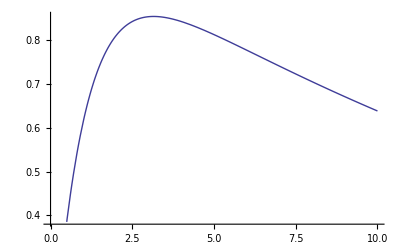

```mathematica
Plot[cb[t,.05k1],{t,0,10}]
```

```mathematica
The idea is that for the same spacetime, you would need a very large reactor to make any appreciable amount of this stuff.
```